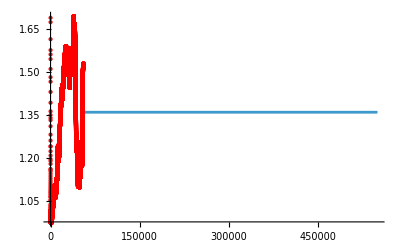

```mathematica
(*============================================================*)
(*1. SETUP:Data Loading and Function Definitions*)
(* ===================================================================*)
(* Read atmospheric 14C data*)
SetDirectory["/Users/flamholz/Documents/workspace/soil_diskin/notebooks"];
C14DATADIR="../data/14C_atm_annot.csv";
C14DATA=Import[C14DATADIR, "HeaderLines"-> 1];
C14DATA= C14DATA[[All,{4,5}]];
(*Interpolate the 14C data, use the mean ratio for extrapolation*)
MeanR = Last[Mean[C14DATA[[-50000;;]]]];
atm14C=Interpolation[C14DATA,InterpolationOrder->0,"ExtrapolationHandler"-> {(MeanR&)}];

(* Plot the results of the interpolation to see it makes sense *)
Plot[atm14C[x],{x,0,550000},Epilog->{PointSize[Medium],Red,Point[C14DATA]}]
```

```mathematica
(* Define the function that calculates the radiocarbon signal from the inputs of the turnover time and mean age of the system *)
LognormalRadiocarbon[tau_,age_] := (
sig = Sqrt[Log[age/tau]];
mu = -Log[Sqrt[tau^3/age]];
r = NIntegrate[ atm14C[a]*Exp[-a/8267]* PDF[LogNormalDistribution[mu,sig],x] * Exp[-x*a] / Exp[-mu+(sig^2)/2],{x,0,Infinity},{a,0,Infinity}, PrecisionGoal->3];
r
)

(* Define the function that optimizes the mean age for a given turnover time and observed radiocarbon signal *)
FindOptimalAge[tau_?NumericQ,rtrue_?NumericQ,InitialAge_?NumericQ]:=(
Module[{objectiveFunction,solution},
(*Define the objective function to minimize:the squared difference between the function output and r_true*)
objectiveFunction[age_?NumericQ]:=(LognormalRadiocarbon[tau,age]-rtrue)^2;
(*Use FindMinimum to find the age that minimizes the objective function*)
(*FindMinimum requires a starting point for'age'*)
solution=Quiet[FindMinimum[objectiveFunction[age],{age,InitialAge}, AccuracyGoal->8, MaxIterations->100]];
(*solution=FindMinimum[objectiveFunction[age],{age,InitialAge}, AccuracyGoal->8, MaxIterations->100];*)
(*Return the value of age that minimizes the difference*)
Return[age/. Last[solution]]]
)

csvFilePath = "../results/tropical_sites_14C_turnover.csv"
Print["Importing data from: ",csvFilePath];
data=Import[csvFilePath,"Dataset",HeaderLines->1];
data = Values[data[[All,{"turnover","fm"}]]]//Normal;
```

../results/tropical_sites_14C_turnover.csv

Importing data from: ../results/tropical_sites_14C_turnover.csv

```mathematica
LaunchKernels[];

(*3. Distribute definitions to parallel kernels*)
(*Make sure all symbols that FindOptimalAge and LognormalRadiocarbon depend on are distributed.*)
(*atm14C is already defined globally.If it were a more complex structure or function,you'd want to be sure it's available.*)
DistributeDefinitions[LognormalRadiocarbon,FindOptimalAge,atm14C];

agelist = 10^Range[3,5.5, (5.5-3)/100];
ScanAges[tau_] := Module[{ages}, ages =Table[Quiet[LognormalRadiocarbon[tau, i]],{i,agelist}];
Return[ages]]
```

LaunchKernels::nodef: Some parallel subkernels are already running. Not launching default kernels again.

```mathematica
results=ParallelMap[ScanAges[#]&,data[[All,1]]]
Export["../results/03b_lognormal_model_age_scan.csv",results,"CSV"]
```

{{1.0448,1.04204,1.0393,1.03653,1.03374,1.03092,1.02843,1.02524,1.02237,1.01966,1.01674,1.01365,1.01068,1.0077,1.00472,1.00167,0.998628,0.995561,0.99252,0.989373,0.986292,0.983171,0.980045,0.976869,0.974,0.970438,0.967169,0.963931,0.960674,0.957764,0.954256,0.950919,0.94761,0.94428,0.940993,0.937574,0.934208,0.930826,0.927424,0.924019,0.92059,0.917169,0.91372,0.910267,0.906803,0.903402,0.899923,0.896431,0.892918,0.889401,0.885883,0.882347,0.878814,0.875271,0.871767,0.86816,0.864597,0.966603,0.962248,0.853866,0.850282,0.846693,0.8431,0.839503,0.835899,0.832297,0.82869,0.825076,0.821459,0.817845,0.814241,0.810621,0.807,0.803396,0.799777,0.796154,0.792532,0.788914,0.785295,0.781676,0.778057,0.774434,0.770819,0.767202,0.763587,0.759973,0.756364,0.752757,0.749155,0.745555,0.741966,0.738367,0.734779,0.731196,0.72762,0.724044,0.720474,0.716912,0.713357,0.709811,0.706261},{1.04309,1.0396,1.03681,1.03398,1.0311,1.02823,1.0255,1.02259,1.01949,1.01653,1.0136,1.0106,1.00759,1.00455,1.0015,0.998426,0.995324,0.992218,0.989097,0.985965,0.982786,0.979604,0.976353,0.973056,0.96981,0.966893,0.963527,1.09093,0.956814,0.95335,0.950008,0.946649,0.943276,0.939985,0.936586,0.933175,0.929749,0.926327,0.922877,0.919409,0.915943,0.912456,0.908976,0.905472,0.901958,0.898418,0.894862,0.891331,0.887783,0.884269,0.880701,0.877126,0.873594,0.870136,0.866352,0.862749,0.859164,0.855522,0.851904,0.84828,0.948392,0.841022,0.837388,0.833748,0.830105,0.82646,0.822809,0.819155,0.815518,0.811865,0.808207,0.80457,0.800914,0.797256,0.793606,0.789949,0.786298,0.782639,0.778984,0.775331,0.77168,0.768029,0.76438,0.760732,0.757091,0.75345,0.74981,0.746177,0.742548,0.738924,0.735302,0.731682,0.728068,0.72446,0.720856,0.717258,0.71368,0.710092,0.706521,0.702944,0.699415},{1.05058,1.048,1.04531,1.04269,1.04005,1.03742,1.03474,1.03203,1.02984,1.02652,1.02376,1.02125,1.01813,1.0153,1.01245,1.0097,1.0068,1.00374,1.0008,0.99782,0.994843,0.99187,0.989106,0.98622,0.982916,0.979829,0.976758,0.973685,0.970557,0.96741,0.964937,0.961085,0.957915,0.954701,0.951713,0.948396,0.945142,0.941791,0.938566,0.935285,0.931999,0.928697,0.925377,0.922028,0.918688,0.915348,0.911988,0.908618,0.905233,0.901846,0.898461,0.895066,0.891652,0.888229,0.884765,0.881322,0.877875,0.87442,0.870952,0.867619,0.864008,0.860528,0.857038,0.853544,0.850071,0.846544,0.843037,0.839704,0.836191,0.832493,0.828969,0.825446,0.82192,0.818388,0.814865,0.811332,0.807806,0.804278,0.800747,0.797212,0.793697,0.790163,0.786623,0.783087,0.779554,0.776018,0.772483,0.768954,0.765422,0.76189,0.75836,0.754831,0.751305,0.747784,0.744267,0.740751,0.73724,0.733736,0.730233,0.726731,0.723232},{1.0318,1.02879,1.02576,1.0227,1.0196,1.0165,1.01339,1.01023,1.00707,1.00387,1.00086,0.997596,0.994357,0.991085,0.987334,0.984282,0.980953,0.977605,0.974243,0.971018,0.967449,0.964028,0.960607,0.957135,0.95366,0.950166,0.946665,0.943148,0.939549,0.936051,0.932489,0.928913,0.925321,0.921728,0.918111,0.914477,0.910835,0.907409,0.903512,0.899844,0.896151,0.892462,0.888763,0.884979,0.881307,0.877577,0.87387,0.870102,0.866355,0.862597,0.858839,0.855075,0.851293,0.847567,0.843787,0.840027,0.836243,0.832451,0.828653,0.824854,0.821053,0.817249,0.813451,0.809649,0.80585,0.802046,0.798248,0.794451,0.790648,0.786848,0.783083,0.779287,0.77549,0.771694,0.767902,0.764116,0.760328,0.756521,0.752752,0.748969,0.745198,0.74143,0.737666,0.733908,0.730154,0.726406,0.722663,0.718929,0.71522,0.711496,0.707777,0.704064,0.700367,0.696672,0.692983,0.6893,0.685626,0.681969,0.678257,0.674609,0.670964},{1.03989,1.03746,1.03418,1.03129,1.02856,1.02563,1.02251,1.01954,1.01655,1.01352,1.01049,1.00743,1.00442,1.0013,0.998202,0.995094,0.991951,0.988805,0.98561,0.982394,0.979098,0.975809,0.972544,0.969234,1.10143,0.962597,0.959405,0.955922,0.952556,0.94924,0.945713,0.942303,0.938876,0.935448,0.93198,0.928513,0.925033,0.921552,0.918049,0.914627,0.911112,0.907676,0.904123,0.900554,0.896974,0.8934,0.889825,0.886227,0.882628,0.879231,0.87545,0.871772,0.868142,0.864531,0.860885,0.85726,0.853608,0.849951,0.846289,0.842621,0.838949,0.835274,0.933062,0.827917,0.824238,0.820555,0.816869,0.81318,0.809491,0.805818,0.802125,0.798435,0.794735,0.791048,0.78736,0.783671,0.779982,0.776293,0.772606,0.76892,0.765238,0.761557,0.75788,0.754203,0.750533,0.746867,0.743203,0.739543,0.735887,0.732234,0.72858,0.724936,0.721303,0.717688,0.714063,0.710442,0.706828,0.703219,0.699613,0.696019,0.692426},{1.04085,1.03803,1.0356,1.03233,1.02945,1.02671,1.02378,1.02066,1.0177,1.0147,1.01169,1.0087,1.00566,1.00258,0.999484,0.996374,0.993269,0.990129,0.98699,0.984411,0.980536,0.977293,0.974004,0.970741,0.967551,1.09785,0.960942,0.957603,0.954259,0.950826,0.947494,0.944039,0.940634,0.937218,0.933786,0.930339,0.926971,0.92353,0.92005,0.916551,0.913051,0.909539,0.906014,0.902474,0.898904,0.895614,0.891789,0.888214,0.884631,0.881041,0.877744,0.874085,0.87022,0.86665,0.863048,0.859418,0.855758,0.852115,0.84847,0.844819,0.84117,0.940362,0.833846,0.830182,0.826518,0.82284,0.819183,0.81551,0.811835,0.808158,0.804498,0.800821,0.797142,0.793465,0.789786,0.786111,0.782434,0.778759,0.775084,0.771412,0.76774,0.764071,0.760404,0.756741,0.753078,0.749419,0.745767,0.742117,0.738476,0.734834,0.731188,0.727558,0.723932,0.720307,0.716706,0.713094,0.709489,0.705889,0.702295,0.698699,0.695118},{1.0354,1.03227,1.02923,1.02624,1.02372,1.02069,1.01763,1.01456,1.01149,1.00833,1.00527,1.00217,0.999035,0.995835,0.992504,0.989075,0.985604,0.982331,0.979041,0.975725,1.11624,0.969034,0.965834,0.962295,0.958892,0.955542,0.952044,0.948583,0.945115,0.941634,0.938141,0.934634,0.931111,0.927576,0.924031,0.920471,0.916893,0.913315,0.90967,0.90605,0.902424,0.899015,0.895368,0.891497,0.887855,0.884191,0.880579,0.876882,0.873198,0.869529,0.865802,0.862105,0.858318,0.854597,0.850875,0.847145,0.843414,0.839681,0.835942,0.832199,0.828453,0.824971,0.820968,0.817215,0.913105,0.809741,0.805983,0.802231,0.798483,0.79472,0.790975,0.78722,0.783468,0.779715,0.775964,0.772218,0.768478,0.764734,0.760992,0.757248,0.753513,0.749779,0.746054,0.742332,0.73861,0.734896,0.731184,0.72748,0.723779,0.720075,0.716388,0.712705,0.709041,0.705372,0.701703,0.698046,0.694396,0.690758,0.687185,0.683495,0.679881},{1.04516,1.04245,1.03969,1.03692,1.03414,1.03133,1.02884,1.02567,1.0228,1.02011,1.01719,1.01411,1.01115,1.00818,1.00521,1.00219,0.999156,0.996098,0.993017,0.989922,0.986833,0.983717,0.980604,0.978,0.97455,0.971027,0.967764,0.964533,0.961284,0.95824,0.954917,0.951627,0.948259,0.944938,0.94166,0.938249,0.93489,0.931517,0.928124,0.924726,0.921307,0.917881,0.914453,0.911007,0.907618,0.904166,0.900696,0.897203,0.893703,0.890197,0.886675,0.883154,0.879618,0.87609,0.872686,0.868993,0.865437,0.967442,0.858521,0.85475,0.851149,0.847566,0.843979,0.840389,0.836793,0.833193,0.829595,0.825987,0.82238,0.818768,0.815172,0.811555,0.80794,0.804342,0.800725,0.797105,0.793495,0.78988,0.786268,0.782653,0.779041,0.775421,0.771812,0.768201,0.76459,0.76098,0.757376,0.753774,0.750174,0.746579,0.742994,0.739402,0.735815,0.732248,0.728672,0.725092,0.721525,0.717963,0.714415,0.710867,0.707325},{1.0336,1.03063,1.02762,1.02459,1.02154,1.01848,1.01539,1.01273,1.00961,1.00646,1.00323,1.00009,0.996963,0.99315,0.9901,0.986608,0.983333,0.980024,0.97669,1.11984,0.969968,0.966579,0.963113,0.959841,0.956327,0.952871,0.949405,0.945919,0.942408,0.938895,0.935368,0.931825,0.92827,0.9247,0.921128,0.91753,0.913928,0.9102,0.906668,0.903212,0.899372,0.895658,0.891988,0.888309,0.884751,0.880947,0.877238,0.873529,0.869839,0.866071,0.862401,0.858664,0.854922,0.851187,0.847438,0.843681,0.839919,0.836172,0.8324,0.82863,0.824852,0.821077,0.817304,0.813524,0.809745,0.904366,0.80219,0.798452,0.794678,0.790899,0.78712,0.783345,0.779506,0.77574,0.771974,0.768205,0.764439,0.760674,0.756913,0.753159,0.749403,0.745654,0.741907,0.738165,0.73443,0.730699,0.726971,0.723251,0.719528,0.715819,0.71213,0.708434,0.704744,0.701055,0.697379,0.693715,0.690048,0.686393,0.682748,0.679108,0.675487},{1.03572,1.03251,1.02956,1.02707,1.02407,1.02104,1.018,1.01493,1.01183,1.0088,1.00567,1.00257,0.999401,0.996217,0.993002,0.990435,0.986038,0.982771,0.979489,0.976181,1.11628,0.741563,0.966153,0.962774,0.959378,0.956024,0.952545,0.949089,0.945477,0.942151,0.938667,0.935166,0.931651,0.928123,0.924582,0.92102,0.917461,0.913885,0.910246,0.906632,0.903016,0.899677,0.895877,0.892104,0.888467,0.884807,0.881265,0.877514,0.873835,0.870099,0.866415,0.862686,0.858977,0.855261,0.851545,0.847821,0.844094,0.840366,0.836632,0.832894,0.829152,0.825422,0.821677,0.817929,0.913879,0.810468,0.806715,0.802955,0.799213,0.795472,0.791721,0.787971,0.784221,0.780474,0.776729,0.772982,0.76924,0.765508,0.76177,0.758029,0.754298,0.75057,0.746845,0.743126,0.73941,0.735697,0.731988,0.728286,0.724587,0.720888,0.717204,0.713527,0.709862,0.706194,0.702529,0.698874,0.695226,0.691591,0.688019,0.684333,0.68072},{1.04834,1.04571,1.04307,1.0403,1.0376,1.03488,1.03213,1.02936,1.02657,1.02407,1.02092,1.01806,1.01532,1.01244,1.00937,1.00643,1.00347,1.00049,0.997491,0.994479,0.991442,0.988385,0.985314,0.982527,0.979117,0.975985,0.972827,0.969684,0.96648,0.963288,0.960219,0.957007,0.95404,0.950639,0.947389,0.944553,0.940731,0.937324,1.05357,0.930714,0.92737,0.924018,0.920652,0.917273,0.913883,0.910484,0.907075,0.903653,0.900233,0.896797,1.00363,0.999211,0.99502,0.991056,0.879457,0.875959,0.872464,0.869101,0.865454,0.86194,0.858418,0.854913,0.851378,0.848023,0.844279,0.840735,0.837185,0.833632,0.830069,0.826508,0.822953,0.819393,0.815826,0.812272,0.808701,0.805138,0.801575,0.798,0.794439,0.790866,0.787294,0.783725,0.780154,0.776589,0.773019,0.769455,0.765888,0.762332,0.758769,0.755208,0.751651,0.748096,0.744546,0.740997,0.737453,0.733915,0.730378,0.726845,0.72332,0.719795,0.716276},{1.03106,1.02803,1.02499,1.02187,1.01877,1.01566,1.01251,1.00935,1.00616,1.00316,0.999953,0.996702,0.993402,0.989913,0.986354,0.983274,0.979929,1.12812,0.973193,0.969784,0.966364,0.963007,0.959489,0.956002,0.952507,0.949008,0.94549,0.941956,0.938409,0.934828,0.931252,0.92766,0.924064,0.920443,0.916809,0.913384,0.909732,0.905841,0.90216,0.898476,0.894772,0.891068,0.887474,0.883644,0.879875,0.876131,0.872412,0.868629,0.864873,0.861104,0.857332,0.853551,0.849759,0.845971,0.842177,0.838445,0.834656,0.830853,0.827041,0.823232,0.819423,0.815609,0.811799,0.807986,0.804177,0.800364,0.893407,0.792747,0.788942,0.785131,0.781321,0.777545,0.773739,0.769934,0.766137,0.762338,0.758521,0.754731,0.750944,0.747156,0.743377,0.739601,0.735834,0.732069,0.728309,0.724553,0.720808,0.717084,0.713347,0.709617,0.705893,0.702183,0.698471,0.694772,0.691076,0.68739,0.683712,0.680038,0.676376,0.672722,0.669076},{1.03575,1.03254,1.02959,1.0271,1.0241,1.02107,1.01803,1.01496,1.01187,1.00884,1.00566,1.0026,0.999435,0.996252,0.993037,0.990468,0.986074,0.982808,0.979526,0.976219,1.11629,0.741655,0.966192,0.962814,0.959418,0.956065,0.952587,0.949132,0.945522,0.942199,0.938711,0.935209,0.931696,0.928169,0.924628,0.921068,0.917508,0.913933,0.910294,0.90668,0.903065,0.899727,0.895927,0.892154,0.888518,0.884858,0.881319,0.877566,0.873809,0.870152,0.866469,0.862742,0.859033,0.855317,0.851601,0.847877,0.844151,0.840423,0.836686,0.832952,0.82921,0.825481,0.821737,0.817989,0.913944,0.810529,0.806776,0.803017,0.799275,0.795535,0.791784,0.788034,0.784285,0.780538,0.776792,0.773046,0.769305,0.765572,0.761835,0.758094,0.754363,0.750636,0.746912,0.743192,0.739477,0.735764,0.732056,0.728354,0.724655,0.720956,0.717273,0.713595,0.709931,0.706263,0.702598,0.698943,0.695296,0.69166,0.688088,0.684403,0.68079},{1.06263,1.05987,1.05762,1.05535,1.05308,1.05078,1.04845,1.04635,1.04402,1.04163,1.03922,1.03679,1.03433,1.03189,1.02937,1.02685,1.02432,1.02176,1.0194,1.01681,1.01397,1.01133,1.00909,1.006,1.0033,1.00081,0.997865,0.99511,0.992345,0.989557,0.986846,0.984028,0.981192,0.978245,0.975382,0.97249,0.969594,0.96665,0.963716,0.960779,0.958228,0.954876,0.951862,0.948867,0.945823,0.94279,0.939773,0.936686,0.933851,0.930605,0.927508,0.924307,0.921219,0.91808,0.91494,0.911793,0.908633,0.905466,0.902248,0.899069,0.895871,0.892667,0.889439,0.886216,0.882996,0.879814,0.876694,0.873458,0.870235,0.866973,0.863628,0.860184,0.856901,0.853717,0.850322,0.847047,0.843716,0.840413,0.83712,0.833807,0.830488,0.82716,0.823845,0.820519,0.817189,0.813857,0.810511,0.807176,0.803837,0.800498,0.797158,0.793817,0.790498,0.787289,0.783947,0.78047,0.777138,0.773792,0.770449,0.767126,0.763786},{1.02201,1.01872,1.01562,1.01238,1.00912,1.0061,1.00279,0.999489,0.996139,0.99253,0.989141,0.985734,1.15163,0.978844,0.975461,0.971898,0.968389,0.964859,0.961311,0.957748,0.954154,0.950547,0.94695,0.943321,0.939894,0.935992,0.932319,0.928614,0.924899,0.921177,0.917433,0.913684,0.909905,0.906131,0.902343,0.898543,0.894744,0.890926,0.887093,0.883296,0.879428,0.875578,0.871709,0.867849,0.863972,0.860092,0.856204,0.852326,0.848427,0.844527,0.840622,0.836713,0.832786,0.828864,0.824945,0.821022,0.817077,0.813153,0.809227,0.805287,0.801362,0.797435,0.793523,0.78959,0.785674,0.78176,0.777839,0.773911,0.862599,0.766117,0.762205,0.758297,0.754395,0.750504,0.746611,0.742721,0.738839,0.734961,0.73109,0.727224,0.723367,0.719522,0.715675,0.711983,0.708017,0.70421,0.700394,0.696588,0.692791,0.688997,0.685216,0.681442,0.677674,0.673907,0.67023,0.666427,0.662698,0.65898,0.655274,0.651576,0.647886},{1.01911,1.01588,1.0127,1.00952,1.00648,1.00315,0.999823,0.9962,0.99281,0.989401,0.98618,1.15721,0.979143,0.975525,0.972009,0.968486,0.964656,0.96136,0.957765,0.95415,0.950525,0.946853,0.943225,0.939557,0.935849,0.932126,0.92839,0.924647,0.920892,0.917125,0.913342,0.909544,0.905737,0.901909,0.898074,0.894233,0.890385,0.886555,0.882648,0.878783,0.874887,0.870992,0.867091,0.86318,0.859268,0.855361,0.851439,0.847473,0.843583,0.839643,0.835695,0.831744,0.827793,0.823836,0.819885,0.815929,0.811962,0.808001,0.804035,0.800053,0.796088,0.792137,0.788179,0.784224,0.780276,0.776324,0.772381,0.768424,0.764479,0.760501,0.756601,0.752671,0.748773,0.74485,0.740932,0.737017,0.733113,0.729214,0.725319,0.721439,0.717568,0.713695,0.709834,0.705972,0.70212,0.698282,0.694449,0.690743,0.686805,0.683015,0.679214,0.675424,0.671641,0.667867,0.664105,0.660357,0.656615,0.652886,0.64917,0.64546,0.641764},{1.01918,1.01595,1.01277,1.0096,1.00655,1.00323,0.999898,0.996276,0.992887,0.989479,0.986257,1.1572,0.979225,0.975607,0.972093,0.968576,0.96474,0.961447,0.957853,0.954239,0.950614,0.947192,0.943317,0.93965,0.935944,0.932222,0.928487,0.924744,0.920991,0.917225,0.913443,0.909646,0.90584,0.902013,0.89818,0.894339,0.890492,0.886664,0.882757,0.878895,0.874999,0.871104,0.867204,0.863294,0.859384,0.855478,0.851557,0.847592,0.843703,0.839764,0.835817,0.831866,0.827917,0.82396,0.82001,0.816055,0.812088,0.808129,0.804165,0.800182,0.79622,0.792269,0.788311,0.784367,0.780401,0.776458,0.77251,0.76856,0.764616,0.760638,0.756738,0.752809,0.748912,0.744989,0.741072,0.737157,0.733254,0.729355,0.725461,0.721582,0.717711,0.713839,0.709978,0.706117,0.702266,0.698428,0.694594,0.690769,0.686952,0.683162,0.679361,0.675572,0.671789,0.668016,0.664254,0.660506,0.656764,0.653036,0.64932,0.645612,0.641915},{1.02368,1.02053,1.01735,1.01414,1.01091,1.00766,1.00462,1.00134,0.998027,0.994697,0.991096,0.987716,0.984326,1.14654,0.977448,0.974091,0.970517,0.967021,0.963499,0.959967,0.956399,0.952824,0.949253,0.945653,0.942018,0.938382,0.93496,0.931071,0.927389,0.923684,0.919974,0.916235,0.912497,0.908749,0.904992,0.901231,0.897447,0.893657,0.88986,0.886053,0.882264,0.878417,0.874572,0.870693,0.866882,0.863028,0.859167,0.8553,0.851441,0.847554,0.843674,0.839787,0.835896,0.831993,0.828072,0.824168,0.820265,0.81637,0.812457,0.808547,0.804642,0.80074,0.796781,0.792936,0.789033,0.78513,0.781263,0.77737,0.866544,0.769569,0.765677,0.761787,0.7579,0.754018,0.750143,0.746271,0.742404,0.738538,0.734683,0.730831,0.726987,0.723151,0.719341,0.715518,0.711701,0.707897,0.704089,0.700296,0.696509,0.692728,0.688958,0.685195,0.681437,0.677689,0.673943,0.670214,0.666494,0.66279,0.659089,0.6554,0.65172},{1.05558,1.05315,1.0507,1.04824,1.04574,1.04322,1.04068,1.03837,1.03579,1.03319,1.03056,1.02793,1.02525,1.02257,1.01986,1.01714,1.0144,1.01186,1.00882,1.00601,1.00318,1.0007,0.997576,0.994694,0.991674,0.988753,0.985811,0.982854,0.979891,0.976868,0.973915,0.970902,0.968007,0.964962,0.961894,0.958799,0.9557,0.952601,0.94945,0.946283,0.943323,0.940063,0.936889,0.933608,0.930432,0.927214,0.923981,0.920738,0.917487,0.914174,0.910903,0.907617,0.904328,0.901024,0.897619,0.894302,0.890994,0.887666,0.884324,0.880963,0.877588,0.874217,0.870837,0.867456,0.864069,0.860792,0.857294,0.853892,0.850481,0.847067,0.843668,0.840244,0.836801,0.833385,0.82995,0.826495,0.823056,0.819782,0.816331,0.812718,0.80927,0.805826,0.802389,0.798945,0.795495,0.792042,0.788588,0.785134,0.78168,0.778228,0.774779,0.771328,0.767876,0.764431,0.760982,0.757533,0.754087,0.750642,0.747202,0.743765,0.740329},{1.05546,1.05303,1.05058,1.04811,1.04561,1.04308,1.04055,1.03798,1.03565,1.03303,1.0304,1.02777,1.02508,1.02241,1.01971,1.01697,1.01422,1.01168,1.00863,1.00582,1.00299,1.00051,0.997376,0.994371,0.991467,0.988542,0.985596,0.982638,0.979669,0.976643,0.973687,0.97069,0.967755,0.964719,0.961646,0.958551,0.955462,0.952329,0.949191,0.946022,0.943167,0.939795,0.936617,0.933333,0.930153,0.926932,0.923697,0.92045,0.917193,0.91388,0.910605,0.907316,0.904025,0.900717,0.897309,0.893994,0.890678,0.887342,0.883998,0.880638,0.877259,0.873887,0.870504,0.86712,0.863726,0.860395,0.856952,0.853544,0.850131,0.846735,0.843314,0.839868,0.836442,0.833023,0.829586,0.826128,0.822685,0.81941,0.815957,0.812342,0.808891,0.805446,0.802008,0.798561,0.795108,0.791653,0.788197,0.784741,0.781286,0.777831,0.774381,0.770928,0.767474,0.764026,0.760576,0.757126,0.753677,0.75023,0.746789,0.74335,0.739912},{1.04421,1.04144,1.03869,1.0359,1.03309,1.03061,1.02743,1.02456,1.02183,1.0189,1.01586,1.01291,1.00991,1.00691,1.0039,1.00087,0.997807,0.994744,0.991645,0.988548,0.985437,0.982315,0.97971,0.975932,0.973004,0.969451,0.966212,0.96296,0.95992,0.956549,0.953199,0.949887,0.946563,0.943278,0.939859,0.936486,0.933108,0.929712,0.926299,0.922874,0.919445,0.915999,0.912546,0.90908,0.905616,0.902125,0.898692,0.895168,0.891661,0.888131,0.884603,0.881056,0.877508,0.874047,0.870389,0.866821,0.863444,0.859684,0.960926,0.852484,0.848888,0.845287,0.841685,0.838076,0.834466,0.830851,0.827229,0.823609,0.819985,0.816375,0.812745,0.809116,0.805503,0.801874,0.798239,0.794614,0.790986,0.787359,0.78373,0.780103,0.77647,0.772846,0.769221,0.765597,0.761971,0.758352,0.754739,0.751124,0.747515,0.743915,0.74031,0.736711,0.733115,0.729523,0.72593,0.722364,0.718789,0.715222,0.711667,0.708106,0.704551},{1.03099,1.02796,1.02491,1.02179,1.01869,1.01557,1.01242,1.00926,1.00604,1.00308,0.999862,0.99661,0.993309,0.989819,0.986257,0.983176,0.97983,1.1281,0.973092,0.96968,0.966258,0.962901,0.959381,0.955893,0.952396,0.948895,0.945377,0.941841,0.938292,0.93471,0.931132,0.927539,0.923942,0.920319,0.916683,0.913257,0.909603,0.905712,0.90203,0.898345,0.894638,0.890933,0.887338,0.883506,0.879781,0.875991,0.87219,0.868488,0.864726,0.86096,0.857185,0.853404,0.84961,0.845822,0.842027,0.838292,0.834503,0.830699,0.826885,0.823075,0.819266,0.815458,0.811639,0.807829,0.804015,0.800206,0.893226,0.792582,0.788776,0.784964,0.781151,0.777377,0.77357,0.769764,0.765966,0.762166,0.758348,0.754558,0.75077,0.746981,0.743202,0.739426,0.735657,0.731891,0.728131,0.724374,0.720629,0.716904,0.713166,0.709435,0.705711,0.702,0.698288,0.694589,0.690892,0.687206,0.683527,0.679853,0.676191,0.672536,0.668888},{1.02873,1.02565,1.02256,1.01945,1.0163,1.01305,1.00987,1.00646,1.00367,1.00041,0.997138,0.99385,0.990335,0.987006,0.98365,0.980616,0.976898,0.973488,0.97006,0.966702,0.963157,0.959667,0.956174,0.952637,0.949102,0.945559,0.942,0.938421,0.934827,0.93122,0.927591,0.923965,0.920535,0.916638,0.912968,0.90928,0.905585,0.901878,0.89816,0.894433,0.890684,0.88701,0.883207,0.879447,0.875699,0.87189,0.868103,0.864314,0.860485,0.856677,0.852868,0.849052,0.845163,0.841424,0.837596,0.833758,0.82993,0.826089,0.822019,0.818454,0.814614,0.810771,0.806928,0.803086,0.799241,0.795411,0.791569,0.787727,0.783886,0.780047,0.77621,0.772377,0.768548,0.764719,0.760892,0.757077,0.753259,0.749443,0.745629,0.741824,0.738025,0.734228,0.730436,0.726651,0.722865,0.719105,0.715348,0.711586,0.70784,0.70409,0.700348,0.696616,0.692892,0.689176,0.68547,0.681767,0.67812,0.674386,0.670704,0.667039,0.663383},{1.04347,1.0414,1.03794,1.03515,1.03232,1.02948,1.02661,1.02373,1.02098,1.01791,1.01495,1.01197,1.00899,1.00597,1.00295,0.999898,0.996839,0.993744,0.990618,0.987509,0.98441,0.981229,0.978057,0.974812,0.971848,0.968312,0.965032,0.962017,0.958629,0.955322,0.951872,0.948641,0.945297,0.941939,0.938562,0.935175,0.93178,0.92837,0.924938,0.921504,0.918057,0.914599,0.911128,0.907652,0.904158,0.901073,0.89714,0.893675,0.890137,0.886606,0.883047,0.879498,0.875938,0.872419,0.868988,0.865406,0.861616,0.858043,0.85442,0.954923,0.847207,0.843596,0.83998,0.836361,0.832737,0.82911,0.825476,0.821845,0.818223,0.814584,0.810944,0.807304,0.803683,0.800044,0.796396,0.792761,0.789127,0.785487,0.781843,0.778207,0.774568,0.770934,0.767299,0.763666,0.760037,0.75641,0.752784,0.749162,0.74554,0.741935,0.73832,0.734714,0.731112,0.727515,0.723918,0.72033,0.716747,0.713196,0.709623,0.706057,0.702495},{1.04398,1.04124,1.03848,1.03569,1.03288,1.03039,1.0272,1.02433,1.02159,1.01866,1.0156,1.01263,1.00965,1.00664,1.00363,1.00059,0.997537,0.994478,0.991357,0.988259,0.985142,0.982013,0.979422,0.975633,0.972687,0.969129,0.965886,0.962604,0.959584,0.956208,0.952851,0.949534,0.946205,0.942917,0.939493,0.936115,0.932732,0.929334,0.925913,0.922489,0.919053,0.915604,0.912143,0.908671,0.905626,0.901709,0.898273,0.894743,0.891224,0.887698,0.884162,0.880615,0.877065,0.873652,0.869936,0.866562,0.862983,0.85922,0.960474,0.955904,0.848413,0.844808,0.841201,0.837589,0.833978,0.830359,0.826733,0.82311,0.819497,0.815866,0.812234,0.808602,0.804989,0.801356,0.797718,0.79409,0.790461,0.786829,0.783197,0.779562,0.775932,0.772305,0.768677,0.76505,0.761422,0.757803,0.754184,0.750568,0.746956,0.743354,0.739747,0.736147,0.732549,0.728954,0.725359,0.721791,0.718214,0.714645,0.711088,0.707526,0.703969},{1.04398,1.04124,1.03848,1.03569,1.03288,1.03039,1.0272,1.02433,1.02159,1.01866,1.0156,1.01263,1.00965,1.00664,1.00363,1.00059,0.997537,0.994478,0.991357,0.988259,0.985142,0.982013,0.979422,0.975633,0.972687,0.969129,0.965886,0.962604,0.959584,0.956208,0.952851,0.949534,0.946205,0.942917,0.939493,0.936115,0.932732,0.929334,0.925913,0.922489,0.919053,0.915604,0.912143,0.908671,0.905626,0.901709,0.898273,0.894743,0.891224,0.887698,0.884162,0.880615,0.877065,0.873652,0.869936,0.866562,0.862983,0.85922,0.960474,0.955904,0.848413,0.844808,0.841201,0.837589,0.833978,0.830359,0.826733,0.82311,0.819497,0.815866,0.812234,0.808602,0.804989,0.801356,0.797718,0.79409,0.790461,0.786829,0.783197,0.779562,0.775932,0.772305,0.768677,0.76505,0.761422,0.757803,0.754184,0.750568,0.746956,0.743354,0.739747,0.736147,0.732549,0.728954,0.725359,0.721791,0.718214,0.714645,0.711088,0.707526,0.703969},{1.04344,1.04138,1.03791,1.03512,1.03229,1.02945,1.02658,1.0237,1.02091,1.01787,1.01492,1.01194,1.00895,1.00593,1.00291,0.999857,0.996797,0.993702,0.990574,0.987487,0.984365,0.981183,0.977986,0.974765,0.971801,0.968264,0.964983,0.961973,0.958578,0.955271,0.95182,0.948588,0.945244,0.941885,0.938507,0.935119,0.931724,0.928313,0.924893,0.921446,0.917998,0.914539,0.911068,0.907594,0.904096,0.90101,0.897077,0.893612,0.890074,0.886541,0.882982,0.879432,0.875872,0.872352,0.86892,0.865338,0.861548,0.857974,0.854351,0.954854,0.847137,0.843524,0.839908,0.836289,0.832664,0.829037,0.825402,0.821769,0.818148,0.814509,0.810868,0.807228,0.803606,0.799966,0.796318,0.792684,0.789048,0.785408,0.781763,0.778127,0.774488,0.770853,0.767218,0.763585,0.759955,0.756328,0.752702,0.74908,0.745457,0.741851,0.738236,0.73463,0.731027,0.72743,0.723833,0.720245,0.716676,0.71311,0.709537,0.70597,0.702409},{1.04469,1.04193,1.03984,1.03641,1.03362,1.03081,1.02831,1.02511,1.02224,1.01953,1.0166,1.01351,1.01054,1.00755,1.00457,1.00152,0.99847,0.995404,0.99232,0.989217,0.986128,0.983031,0.979876,0.976697,0.973806,0.970261,0.966989,0.963748,0.96071,0.957577,0.954066,0.950726,0.947413,0.944081,0.94079,0.937369,0.934001,0.930617,0.927212,0.923804,0.920375,0.916951,0.913501,0.910043,0.90659,0.903172,0.899691,0.896196,0.892681,0.889168,0.885643,0.882102,0.878569,0.875023,0.871517,0.867908,0.864536,0.966358,0.961999,0.853606,0.85002,0.846428,0.842833,0.839235,0.835628,0.832024,0.828416,0.8248,0.821181,0.817581,0.813959,0.810338,0.806716,0.803109,0.799489,0.795864,0.792241,0.788621,0.785,0.781379,0.77776,0.774135,0.770518,0.7669,0.763283,0.759668,0.756058,0.75245,0.748846,0.745252,0.741651,0.738055,0.734469,0.730881,0.727304,0.723726,0.720155,0.716592,0.713039,0.70949,0.70594},{1.04265,1.03988,1.03709,1.03427,1.03178,1.02853,1.02565,1.0229,1.01982,1.01685,1.01393,1.01094,1.00793,1.0049,1.00186,0.998794,0.995704,0.992577,0.989466,0.986362,0.983185,0.980011,0.976801,0.973541,0.97056,0.967315,0.963703,0.960673,0.957131,0.953806,0.950475,0.947117,0.943811,0.940468,0.937076,0.93367,0.930251,0.926829,0.92339,0.919933,0.916462,0.912985,0.909506,0.906009,0.902494,0.898969,0.895426,0.891895,0.888348,0.884849,0.881282,0.877713,0.874185,0.870733,0.867158,0.863356,0.859776,0.856139,0.852526,0.952863,0.948435,0.841658,0.838029,0.834395,0.830755,0.827115,0.823465,0.819821,0.816185,0.812535,0.808883,0.80525,0.801599,0.797948,0.794294,0.790646,0.786997,0.783342,0.779691,0.776041,0.772395,0.768747,0.765101,0.761455,0.757819,0.754181,0.750546,0.746912,0.743288,0.739666,0.736047,0.732433,0.72882,0.725213,0.721612,0.718016,0.714441,0.710866,0.707287,0.703712,0.70014},{1.04355,1.04147,1.03803,1.03523,1.03241,1.02957,1.0267,1.02383,1.02108,1.018,1.01505,1.01208,1.0091,1.00608,1.00306,1.,0.99695,0.993853,0.990733,0.987626,0.984529,0.981349,0.978179,0.974936,0.972011,0.96844,0.965162,0.962149,0.959027,1.08403,0.952009,0.948781,0.945439,0.942083,0.938709,0.935323,0.931929,0.928521,0.925092,0.921658,0.918213,0.914757,0.911288,0.907814,0.90432,0.900834,0.897306,0.893844,0.890307,0.886777,0.883225,0.879673,0.876114,0.872596,0.86897,0.865589,0.861799,0.858228,0.959318,0.955106,0.847397,0.843786,0.840171,0.836554,0.832932,0.829306,0.825673,0.822044,0.818408,0.814785,0.811146,0.807506,0.803888,0.80025,0.796605,0.79297,0.789336,0.785696,0.782059,0.778419,0.774782,0.771149,0.767516,0.763884,0.76025,0.756629,0.753004,0.749383,0.745775,0.742157,0.738544,0.734938,0.731337,0.727742,0.724144,0.720558,0.716986,0.713425,0.709853,0.706287,0.702726},{1.04197,1.03918,1.03637,1.0339,1.03064,1.02776,1.02503,1.02211,1.019,1.01607,1.01308,1.01007,1.00705,1.00401,1.00095,0.997888,0.994732,0.991629,0.988498,0.985376,0.982791,0.978958,0.975722,0.97242,0.969164,0.96623,1.09451,0.959292,0.955974,0.952634,0.94928,0.945977,0.942549,0.939158,0.935841,0.932419,0.928986,0.92555,0.922094,0.918616,0.915142,0.911646,0.908149,0.904646,0.901114,0.897562,0.894277,0.890469,0.886908,0.88334,0.879814,0.876326,0.872826,0.869041,0.865431,0.861845,0.858228,0.854581,0.850955,0.847323,0.947413,0.840052,0.836409,0.832761,0.829112,0.82546,0.821801,0.818156,0.814499,0.810838,0.807176,0.803534,0.799874,0.796204,0.792548,0.788891,0.785224,0.781565,0.777905,0.774245,0.770589,0.766933,0.76328,0.759628,0.75598,0.752334,0.748691,0.745055,0.741419,0.73779,0.734167,0.73054,0.726922,0.72331,0.719701,0.716115,0.712518,0.708927,0.705342,0.701771,0.698241},{1.0389,1.03563,1.03275,1.02999,1.02687,1.02392,1.02094,1.01793,1.01491,1.01186,1.00877,1.0057,1.00258,0.99945,0.996379,0.993221,0.990029,0.986821,0.98355,0.980287,0.976939,0.973673,1.10915,1.10472,0.963731,0.960371,0.957006,0.95363,0.950298,0.946823,0.943399,0.939962,0.936447,0.932979,0.929502,0.926004,0.9225,0.91898,0.915459,0.91192,0.908365,0.904875,0.901291,0.89771,0.894119,0.890508,0.887094,0.88347,0.87976,0.876011,0.872369,0.868713,0.865083,0.8614,0.857733,0.854362,0.850377,0.84647,0.843049,0.839359,0.835665,0.831971,0.828273,0.824571,0.820878,0.817171,0.813462,0.809819,0.80611,0.802413,0.798697,0.794981,0.791276,0.787565,0.783858,0.78015,0.776441,0.772735,0.76903,0.765328,0.761629,0.757928,0.75424,0.750548,0.746861,0.743177,0.739499,0.735823,0.732152,0.728487,0.724815,0.721165,0.717532,0.713889,0.710251,0.706619,0.702993,0.699369,0.695754,0.692206,0.688556},{1.04726,1.04462,1.04193,1.03922,1.03642,1.03366,1.03089,1.02809,1.02564,1.02246,1.01959,1.01686,1.01395,1.01089,1.00795,1.00498,1.00199,0.99899,0.995965,0.992921,0.989866,0.98677,0.983661,0.980851,0.977758,0.974294,0.971112,0.967883,0.964613,0.961392,0.958159,0.955127,0.951776,0.948515,0.945342,0.941973,0.938622,0.935238,0.931893,0.92854,0.925241,0.921859,0.918474,0.915078,0.911662,0.908238,0.904806,0.901379,0.897924,0.894464,0.890984,0.887499,0.884003,0.98888,0.984403,0.980111,0.8699,0.866445,0.862915,0.859379,0.855859,0.852504,0.848735,0.845179,0.841619,0.838054,0.834487,0.830913,0.827337,0.823756,0.820181,0.816599,0.81303,0.809444,0.805871,0.802288,0.798696,0.795119,0.791531,0.787943,0.784358,0.780774,0.777189,0.773604,0.770024,0.766437,0.762855,0.759276,0.7557,0.752127,0.74857,0.745003,0.74144,0.737885,0.734328,0.730776,0.727229,0.723686,0.720146,0.716612,0.713082},{1.05043,1.04786,1.04516,1.04254,1.03993,1.03726,1.03458,1.03186,1.02911,1.02635,1.02358,1.02107,1.01794,1.01511,1.01226,1.00951,1.0066,1.00354,1.00059,0.997607,0.994618,0.991617,0.988878,0.985862,0.982691,0.979611,0.976515,0.973438,0.970307,0.967163,0.964665,0.960828,0.957637,0.954441,0.95144,0.94811,0.944865,0.941514,0.938279,0.934991,0.931704,0.928396,0.925048,0.921721,0.918379,0.915034,0.911671,0.908299,0.90491,0.901521,0.898132,0.894733,0.891317,0.88789,0.884419,0.880976,0.877526,0.87407,0.870597,0.867261,0.863648,0.860165,0.856672,0.853197,0.849698,0.846168,0.842667,0.839323,0.83563,0.832107,0.82858,0.825055,0.821523,0.818,0.814467,0.810939,0.807402,0.803873,0.800339,0.796807,0.793269,0.789745,0.786207,0.782666,0.77913,0.775594,0.772057,0.768525,0.764992,0.761458,0.757927,0.754396,0.750867,0.747345,0.743826,0.740309,0.736797,0.73329,0.729786,0.72628,0.722784},{1.04482,1.04207,1.03933,1.03656,1.03377,1.03096,1.02846,1.02527,1.0224,1.0197,1.01677,1.01369,1.01072,1.00774,1.00476,1.0017,0.998663,0.995601,0.992556,0.989415,0.986334,0.983214,0.980089,0.976913,0.974044,0.970483,0.967215,0.963977,0.960721,0.957832,0.954305,0.951017,0.947661,0.944332,0.941045,0.937626,0.934261,0.93088,0.927479,0.924074,0.920646,0.917226,0.913777,0.910325,0.906861,0.90346,0.899982,0.896491,0.892978,0.889462,0.885945,0.88241,0.878877,0.875335,0.871831,0.868225,0.864662,0.966665,0.962312,0.853933,0.85035,0.846761,0.843168,0.839573,0.835968,0.832367,0.828761,0.825147,0.82153,0.817916,0.814313,0.810694,0.807073,0.803469,0.799849,0.796228,0.792607,0.788989,0.78537,0.781752,0.778133,0.774512,0.770896,0.767281,0.763665,0.760051,0.756442,0.752836,0.749233,0.745634,0.742046,0.738448,0.734859,0.731276,0.727701,0.724125,0.720555,0.716994,0.713442,0.709894,0.706344},{1.04891,1.04628,1.04364,1.04089,1.03821,1.03549,1.03337,1.03001,1.02723,1.02443,1.02193,1.01877,1.01591,1.01317,1.01027,1.0072,1.00425,1.00128,0.998299,0.995304,0.992276,0.989229,0.986189,0.983391,0.979995,0.9769,0.974351,0.97061,0.967618,0.964415,0.961209,0.958003,0.955054,0.951672,0.948997,0.945172,0.941802,0.938507,0.935194,1.05038,1.04638,1.04153,0.921806,0.918439,0.915065,0.911678,0.908281,0.90487,1.013,1.00886,1.00447,1.00031,0.887697,0.884225,0.880758,0.877276,0.873786,0.8703,0.86685,0.863297,0.85979,0.856274,0.852776,0.849246,0.845897,0.84216,0.83862,0.835078,0.831523,0.827978,0.824429,0.82088,0.817322,0.813763,0.810215,0.806654,0.803098,0.79954,0.795981,0.792423,0.788861,0.785295,0.781736,0.778174,0.774617,0.771056,0.767514,0.763959,0.760398,0.756845,0.753292,0.749745,0.746202,0.74266,0.739122,0.735592,0.732058,0.728531,0.725008,0.721492,0.717979},{1.0398,1.03736,1.03408,1.03119,1.02846,1.02535,1.0224,1.01943,1.01644,1.01341,1.01037,1.00731,1.00429,1.00115,0.998075,0.994965,0.991809,0.988671,0.985474,0.982245,0.978917,0.97567,0.972399,0.969087,1.10137,0.962448,0.959112,0.955766,0.952398,0.94908,0.945552,0.942139,0.938711,0.93528,0.931826,0.928341,0.924859,0.921377,0.917871,0.914448,0.910928,0.907395,0.903852,0.90028,0.896782,0.893207,0.88963,0.886031,0.882549,0.879031,0.875198,0.87157,0.867937,0.864324,0.860676,0.857049,0.853395,0.849737,0.846072,0.842403,0.83873,0.835052,0.933318,0.827693,0.824014,0.820328,0.816641,0.812951,0.809261,0.805585,0.801891,0.798199,0.794495,0.79081,0.787121,0.78343,0.779739,0.776049,0.772361,0.768675,0.764991,0.761309,0.757632,0.753953,0.750281,0.746616,0.74295,0.739289,0.735632,0.731979,0.728322,0.724679,0.721043,0.717428,0.713802,0.710181,0.706566,0.702956,0.69935,0.695754,0.692161},{1.04609,1.04339,1.04068,1.03791,1.03515,1.03237,1.02956,1.02696,1.02379,1.02091,1.01817,1.01526,1.01217,1.00921,1.00625,1.00325,1.00025,0.997214,0.994158,0.991109,0.98801,0.984912,0.9818,0.978663,0.975806,0.972298,0.969091,0.965868,0.962655,0.959405,0.956334,0.953011,0.949726,0.94629,0.943048,0.939771,0.936373,0.933016,0.929643,0.926262,0.92286,0.919453,0.916117,0.912685,0.909244,0.905797,0.902345,0.898884,0.895407,0.891912,0.888413,0.884901,0.881383,0.87786,0.874337,0.977637,0.973494,0.863713,0.860158,0.856815,0.853055,0.849464,0.845892,0.842314,0.838735,0.835145,0.831559,0.827969,0.824375,0.820775,0.817177,0.813589,0.809987,0.806389,0.802786,0.799185,0.795587,0.791986,0.788383,0.78478,0.781178,0.777575,0.773975,0.770372,0.766773,0.763175,0.759576,0.755985,0.752394,0.748807,0.745223,0.74166,0.738082,0.734511,0.730944,0.727371,0.723818,0.720263,0.716707,0.713165,0.709632},{1.05359,1.05111,1.0486,1.04607,1.04351,1.04094,1.03835,1.03572,1.03306,1.0304,1.02771,1.02501,1.02228,1.01952,1.01697,1.01445,1.01137,1.00853,1.00568,1.00293,1.00005,0.997279,0.995185,0.991149,0.988186,0.985206,0.982218,0.979213,0.976176,0.973146,0.970035,0.966983,0.96388,0.960767,0.957651,0.954476,0.951328,0.948338,0.945249,0.942002,0.938799,0.935462,0.932277,0.929027,0.925775,0.922493,0.919162,0.915873,0.912574,0.909158,0.905826,0.902495,0.899148,0.895797,0.892462,0.888889,0.885721,0.882324,0.878916,0.875519,0.872111,0.868697,0.865263,0.861884,0.858411,0.854972,0.851523,0.848101,0.844646,0.84117,0.837713,0.834255,0.830769,0.827465,0.823991,0.820368,0.816891,0.813407,0.809931,0.806463,0.802975,0.799497,0.796016,0.792528,0.789043,0.785556,0.782068,0.778587,0.775096,0.771611,0.768129,0.764651,0.761169,0.757685,0.754206,0.75073,0.747259,0.743789,0.740318,0.736852,0.733396},{1.05387,1.05141,1.04889,1.04637,1.04384,1.04127,1.03869,1.03607,1.03342,1.03078,1.02809,1.02538,1.02268,1.02014,1.01739,1.01487,1.0118,1.00897,1.00613,1.00339,1.00051,0.99859,0.994842,0.991639,0.988686,0.985713,0.982723,0.979726,0.976719,0.973688,0.970582,0.968041,0.96445,0.961335,0.958225,0.955068,0.95192,0.948733,0.94591,0.942626,0.939433,0.936108,0.932924,0.92968,0.926428,0.923162,0.919884,0.916557,0.913265,0.909938,0.906537,0.903209,0.899873,0.896527,0.8932,0.889639,0.886471,0.883087,0.879684,0.876292,0.872891,0.869482,0.866057,0.86276,0.859211,0.855778,0.852342,0.848917,0.845475,0.842006,0.838554,0.835106,0.831642,0.828178,0.82486,0.821383,0.817766,0.814287,0.810815,0.807338,0.803874,0.800401,0.796922,0.79344,0.789957,0.786478,0.782994,0.779517,0.776038,0.772557,0.769076,0.765596,0.762121,0.758643,0.755168,0.751696,0.748226,0.74476,0.741299,0.737833,0.73438},{1.04713,1.04448,1.04179,1.03908,1.03627,1.03351,1.03073,1.02793,1.02548,1.02229,1.01942,1.01669,1.01378,1.01071,1.00776,1.00479,1.0018,0.998798,0.99577,0.99272,0.989664,0.986457,0.983452,0.980639,0.977542,0.973956,0.970858,0.967583,0.964385,0.961163,0.957924,0.95489,0.951553,0.94827,0.945092,0.94172,0.938366,0.93498,0.931628,0.928274,0.92497,0.921586,0.918197,0.914798,0.911378,0.907953,0.904518,0.901089,0.897628,0.894171,0.890683,0.887196,0.883696,0.880198,0.98412,0.979823,0.869492,0.866126,0.862594,0.859054,0.855731,0.852178,0.848402,0.844843,0.841281,0.837714,0.834144,0.830568,0.82699,0.823411,0.819829,0.816244,0.812674,0.809086,0.805509,0.801926,0.798331,0.794749,0.791162,0.787572,0.783985,0.7804,0.776812,0.773227,0.769643,0.766055,0.76247,0.75889,0.755313,0.751738,0.748179,0.744612,0.741047,0.73749,0.733931,0.730379,0.726829,0.723284,0.719744,0.716209,0.712677},{1.04097,1.03816,1.03573,1.03246,1.02959,1.02685,1.02393,1.02081,1.01785,1.01485,1.01184,1.00886,1.00582,1.00275,0.999696,0.996507,0.993442,0.990306,0.98717,0.983979,0.980747,0.977481,0.974195,0.970934,0.967656,1.09794,0.961146,0.957809,0.954468,0.951026,0.947706,0.944256,0.940854,0.937441,0.93401,0.930567,0.927202,0.923764,0.920288,0.91679,0.913292,0.909784,0.906266,0.902723,0.899159,0.895603,0.892047,0.888473,0.884894,0.881307,0.878364,0.874355,0.870542,0.866925,0.863325,0.859697,0.856039,0.852399,0.848757,0.845107,0.84146,0.940663,0.834141,0.830479,0.826815,0.823141,0.819486,0.815814,0.812141,0.808466,0.804809,0.801133,0.797456,0.793781,0.790105,0.78643,0.782756,0.779082,0.775409,0.771738,0.768068,0.7644,0.760735,0.757073,0.753411,0.749754,0.746102,0.742454,0.738815,0.735175,0.73153,0.727901,0.724275,0.720652,0.717052,0.713442,0.709836,0.706238,0.702645,0.699051,0.695527},{1.04699,1.04433,1.04164,1.03885,1.03612,1.03336,1.03057,1.02776,1.02531,1.02212,1.01925,1.01652,1.0136,1.01053,1.00758,1.0046,1.00161,0.998598,0.995567,0.992509,0.989463,0.986244,0.983235,0.980419,0.97778,0.973734,0.970639,0.967349,0.964147,0.960919,0.957895,0.954765,0.951298,0.948016,0.944731,0.941365,0.938101,0.93471,0.931355,0.927997,0.924688,0.921302,0.91791,0.914508,0.911086,0.907657,0.904218,0.900776,0.897321,0.893864,0.890595,0.886882,0.883379,0.879882,0.983789,0.979524,0.869163,0.865794,0.862259,0.858717,0.855387,0.851834,0.848057,0.844495,0.840931,0.837361,0.833789,0.83021,0.826635,0.823049,0.819463,0.815877,0.812304,0.808714,0.805134,0.801548,0.797953,0.794369,0.79078,0.787188,0.783599,0.78001,0.776421,0.772836,0.769248,0.765659,0.762072,0.75849,0.754911,0.751333,0.747761,0.744205,0.740639,0.73708,0.73352,0.729966,0.726412,0.722869,0.719327,0.715791,0.712258},{1.04316,1.0404,1.03761,1.03481,1.03232,1.02913,1.02625,1.02349,1.02057,1.01746,1.01456,1.01157,1.00858,1.00556,1.00253,0.999468,0.9964,0.993299,0.990188,0.987066,0.983945,0.981354,0.977566,0.974322,0.971352,0.96812,0.96452,0.961505,0.958124,0.954659,0.95133,0.947993,0.9448,0.941372,0.93799,0.934594,0.931188,0.927775,0.924347,0.920894,0.917439,0.913976,0.910499,0.907028,0.903525,0.900019,0.89648,0.893194,0.88947,0.885925,0.882369,0.878808,0.875338,0.871665,0.868281,0.864692,0.860919,0.857318,0.853689,0.954632,0.846465,0.842848,0.839226,0.835603,0.831972,0.82834,0.824702,0.821065,0.817434,0.813795,0.81015,0.806504,0.802879,0.799234,0.795589,0.791945,0.788303,0.784659,0.781012,0.777369,0.773728,0.770091,0.766451,0.762815,0.759181,0.75555,0.751921,0.748292,0.744671,0.741057,0.737443,0.733833,0.730229,0.726624,0.723029,0.719437,0.715856,0.712297,0.708721,0.705152,0.701588},{1.04615,1.04342,1.0407,1.03794,1.03518,1.0324,1.02959,1.02699,1.02382,1.02094,1.0182,1.01529,1.0122,1.00924,1.00628,1.00329,1.00028,0.997246,0.994194,0.991146,0.988047,0.98495,0.981838,0.978701,0.975826,0.972341,0.969132,0.96592,0.962697,0.959447,0.956377,0.953055,0.94977,0.946334,0.943094,0.939817,0.936419,0.933064,0.929691,0.926311,0.922909,0.919503,0.916167,0.912736,0.909295,0.905849,0.902398,0.898937,0.895461,0.891966,0.888468,0.884956,0.881443,0.877916,0.874394,0.97769,0.973548,0.863771,0.860218,0.856874,0.853115,0.849524,0.845952,0.842375,0.838796,0.835206,0.831622,0.828032,0.824438,0.820838,0.817241,0.813654,0.810051,0.806455,0.802852,0.799251,0.795653,0.792053,0.78845,0.784848,0.781245,0.777643,0.774043,0.77044,0.766842,0.763245,0.759646,0.756055,0.752464,0.748878,0.745294,0.741731,0.738158,0.734583,0.731016,0.727443,0.723891,0.720336,0.71678,0.713239,0.709706},{1.05271,1.0502,1.04767,1.04512,1.04254,1.03994,1.03732,1.03466,1.03198,1.0293,1.02657,1.02384,1.02108,1.01831,1.01578,1.01269,1.00985,1.0072,1.00445,1.00155,0.99852,0.995587,0.992905,0.989661,0.987437,0.983641,0.980666,0.977644,0.974523,0.971461,0.968397,0.965286,0.962163,0.959045,0.955854,0.952668,0.949671,0.946594,0.943194,0.939983,0.936629,0.933554,0.930312,0.927049,0.92374,0.920398,0.917091,0.913699,0.910374,0.907038,0.903692,0.900328,0.896967,0.893615,0.890239,0.886646,0.883436,0.880015,0.876604,0.873182,0.869759,0.866317,0.862918,0.859431,0.855979,0.852523,0.849078,0.845612,0.84212,0.838652,0.835165,0.831849,0.828362,0.824706,0.821215,0.817723,0.814247,0.810745,0.807248,0.803773,0.800272,0.796776,0.793276,0.789772,0.786276,0.782773,0.779273,0.775774,0.772277,0.768777,0.76528,0.761789,0.75829,0.7548,0.75131,0.747823,0.744326,0.740851,0.737369,0.733901,0.730429},{1.05143,1.04876,1.04619,1.04365,1.04104,1.0384,1.03573,1.03304,1.03031,1.02813,1.02484,1.02206,1.01955,1.01645,1.01361,1.01076,1.00802,1.00512,1.00207,0.99914,0.996185,0.993395,0.99068,0.987359,0.984343,0.981328,0.978243,0.975175,0.972107,0.968985,0.965817,0.962718,0.95952,0.956346,0.953146,0.950156,0.946844,0.943601,0.940253,0.937025,0.933766,0.930496,0.927196,0.923892,0.920564,0.917239,0.913907,0.910556,0.907197,0.903821,0.900441,0.897081,0.893684,0.890279,0.886865,0.883416,0.879985,0.87655,0.873107,0.869654,0.86632,0.862729,0.859261,0.855788,0.852307,0.848839,0.845331,0.841836,0.838511,0.835008,0.831327,0.827816,0.824306,0.820792,0.817271,0.813762,0.810243,0.806735,0.803229,0.799713,0.796199,0.792674,0.789152,0.785629,0.782105,0.778585,0.775064,0.771542,0.768024,0.764505,0.760988,0.757473,0.753957,0.750444,0.746936,0.743433,0.739932,0.736435,0.732947,0.729453,0.725964},{1.05146,1.04879,1.04622,1.04368,1.04107,1.03843,1.03576,1.03307,1.03035,1.02817,1.02487,1.02209,1.01959,1.01649,1.01365,1.0108,1.00806,1.00516,1.00211,0.999184,0.996231,0.993442,0.990728,0.987407,0.984391,0.981364,0.978293,0.975232,0.972159,0.969038,0.96587,0.962772,0.959575,0.956402,0.953203,0.950213,0.946902,0.94366,0.940312,0.937085,0.933828,0.930558,0.927259,0.923952,0.920628,0.917304,0.913973,0.910623,0.907265,0.903889,0.90051,0.897137,0.893753,0.89035,0.886936,0.883488,0.880058,0.876624,0.87318,0.869729,0.866395,0.862805,0.859338,0.855865,0.852385,0.848918,0.84541,0.841915,0.838415,0.835088,0.831408,0.827897,0.824387,0.820875,0.817359,0.813846,0.810327,0.80682,0.803315,0.799798,0.796285,0.79276,0.78924,0.785717,0.782194,0.778674,0.775153,0.771632,0.768114,0.764596,0.761079,0.757564,0.754055,0.750539,0.747029,0.743526,0.740025,0.736528,0.733037,0.729547,0.726061},{1.03917,1.03587,1.03303,1.03029,1.02717,1.02423,1.02125,1.01825,1.01523,1.01218,1.00911,1.00603,1.00297,0.999858,0.996739,0.99359,0.990402,0.987192,0.983974,0.980678,0.977419,0.974073,1.10928,1.10493,0.964153,0.960944,0.95744,0.954067,0.950744,0.947276,0.943858,0.940421,0.936915,0.933452,0.929982,0.926489,0.92299,0.919476,0.915954,0.91242,0.908879,0.905399,0.901812,0.898236,0.894652,0.891045,0.887436,0.884026,0.880203,0.876629,0.872936,0.869289,0.86566,0.862006,0.858319,0.854652,0.850976,0.847071,0.843657,0.83997,0.83628,0.83259,0.828894,0.825281,0.821575,0.817873,0.814169,0.810464,0.806759,0.803067,0.799357,0.79564,0.79194,0.788233,0.78453,0.780825,0.777121,0.773417,0.769716,0.766017,0.762322,0.758627,0.754934,0.751251,0.747566,0.743885,0.740209,0.736537,0.732869,0.729205,0.725545,0.721887,0.718258,0.714617,0.710981,0.707351,0.703728,0.700105,0.696492,0.692946,0.689299},{1.04592,1.04322,1.0405,1.03773,1.03481,1.03202,1.02921,1.02676,1.02359,1.0207,1.01795,1.01504,1.01194,1.00898,1.00602,1.00302,1.00001,0.996962,0.993912,0.990876,0.987735,0.984649,0.981533,0.978391,0.975536,0.972038,0.968807,0.965553,0.962363,0.959276,0.9562,0.952701,0.949421,0.94605,0.942729,0.939448,0.936044,0.932685,0.929307,0.925922,0.92252,0.919107,0.915764,0.912328,0.908883,0.905433,0.901977,0.898512,0.89504,0.891529,0.888024,0.884516,0.880994,0.877467,0.873942,0.870456,0.973117,0.968766,0.859965,0.856402,0.852617,0.849044,0.845469,0.841888,0.838306,0.834715,0.831123,0.82753,0.823933,0.820333,0.81673,0.81314,0.809534,0.805934,0.802335,0.798724,0.795124,0.79152,0.787917,0.784309,0.780704,0.777099,0.773498,0.769891,0.76629,0.762687,0.759089,0.755496,0.751902,0.748314,0.744728,0.741153,0.737582,0.73401,0.73044,0.726865,0.723312,0.719748,0.716197,0.712659,0.709117},{1.03487,1.03193,1.02896,1.02596,1.02286,1.02031,1.01728,1.01419,1.01108,1.00785,1.00475,1.00166,0.998514,0.995268,0.991755,0.98842,0.984943,0.981752,0.978443,0.975119,1.11593,0.968417,0.965058,0.961657,0.958241,0.95481,0.951375,0.947905,0.944428,0.940935,0.937437,0.933921,0.930263,0.926848,0.923291,0.919725,0.91614,0.912553,0.908944,0.905272,0.901636,0.898221,0.894344,0.890687,0.887038,0.883474,0.879687,0.875982,0.872346,0.868669,0.864936,0.861232,0.857512,0.853787,0.850057,0.846321,0.842508,0.838771,0.83502,0.83127,0.82752,0.823776,0.820272,0.81626,0.8125,0.808736,0.80501,0.801252,0.797498,0.793729,0.789979,0.786218,0.782457,0.7787,0.774946,0.7712,0.767448,0.763699,0.759949,0.756204,0.752463,0.748728,0.744999,0.741272,0.737545,0.733827,0.730112,0.7264,0.722698,0.718993,0.715297,0.711614,0.707947,0.704274,0.700602,0.696941,0.693294,0.689648,0.68601,0.682374,0.678761},{1.05383,1.05136,1.04885,1.04633,1.0438,1.04122,1.03864,1.03602,1.03337,1.03073,1.02803,1.02533,1.02262,1.02009,1.01732,1.01481,1.01174,1.00891,1.00607,1.00333,1.00045,0.998519,0.994775,0.991572,0.988616,0.985642,0.982651,0.979653,0.976645,0.973612,0.970507,0.967964,0.964371,0.961255,0.958146,0.95499,0.951833,0.948649,0.945827,0.942539,0.939345,0.936019,0.932834,0.929593,0.926336,0.923068,0.91979,0.916461,0.913172,0.90984,0.906437,0.903114,0.899773,0.896426,0.893097,0.889535,0.886365,0.882981,0.879577,0.876184,0.872782,0.869372,0.865946,0.862648,0.859099,0.855665,0.852228,0.848802,0.845359,0.84189,0.838437,0.834988,0.831523,0.828058,0.824735,0.821118,0.817644,0.814164,0.810692,0.807213,0.803749,0.800275,0.796796,0.793313,0.78983,0.78635,0.782865,0.779386,0.775907,0.772424,0.768943,0.765462,0.761986,0.75851,0.755034,0.751561,0.748091,0.744625,0.741161,0.737696,0.734243},{1.05398,1.05152,1.04901,1.0465,1.04396,1.04139,1.03882,1.0362,1.03355,1.03091,1.02823,1.02552,1.02282,1.0203,1.01754,1.01503,1.01196,1.00914,1.0063,1.00356,1.00069,0.998784,0.995025,0.991824,0.988875,0.985905,0.982918,0.979925,0.97692,0.973898,0.97079,0.968249,0.964661,0.961552,0.958445,0.955291,0.952143,0.949117,0.946154,0.942864,0.939673,0.936351,0.933174,0.929929,0.92668,0.92342,0.920142,0.916817,0.913528,0.910225,0.906805,0.90348,0.900146,0.896803,0.893476,0.889925,0.886752,0.883376,0.879976,0.876583,0.873186,0.86978,0.86636,0.863062,0.859518,0.856088,0.85265,0.849211,0.845791,0.842342,0.838868,0.835448,0.831967,0.828504,0.825188,0.821718,0.818098,0.814621,0.811148,0.807676,0.804215,0.800737,0.797262,0.793787,0.790305,0.786827,0.783347,0.779866,0.77639,0.772913,0.769435,0.765955,0.762482,0.759006,0.755533,0.752062,0.748593,0.745129,0.741668,0.738205,0.734751},{1.04361,1.04154,1.03809,1.0353,1.03248,1.02998,1.02678,1.0239,1.02116,1.01802,1.01513,1.01216,1.00918,1.00616,1.00314,1.00009,0.997041,0.993945,0.990827,0.987722,0.984627,0.981448,0.97828,0.975069,0.972114,0.968545,0.965269,0.962257,0.959137,1.08408,0.952122,0.948896,0.945556,0.94226,0.938828,0.935443,0.932052,0.928645,0.925217,0.921784,0.918341,0.914887,0.911419,0.907947,0.904454,0.900969,0.897443,0.893983,0.890451,0.886916,0.883368,0.879817,0.876259,0.872743,0.869117,0.865734,0.86195,0.858379,0.959466,0.955256,0.847552,0.843943,0.840329,0.836713,0.833091,0.829467,0.825835,0.822206,0.818572,0.81495,0.811312,0.807673,0.804056,0.800419,0.796774,0.793141,0.789508,0.78587,0.782233,0.778593,0.774957,0.771324,0.767693,0.764062,0.760429,0.756806,0.753184,0.749564,0.745956,0.74234,0.738729,0.735122,0.731522,0.727927,0.724329,0.720744,0.717173,0.713612,0.710041,0.706476,0.702917},{1.0353,1.03215,1.02919,1.02612,1.02359,1.02055,1.01743,1.01435,1.01129,1.00813,1.00501,1.00193,0.998787,0.995529,0.992244,0.988711,0.985315,0.982049,0.978744,0.975425,1.11616,0.968725,0.965375,0.961976,0.958568,0.955143,0.951713,0.948245,0.944774,0.941285,0.937792,0.934142,0.930755,0.927215,0.923664,0.939682,0.91652,0.912936,0.90929,0.905664,0.902032,0.898624,0.89497,0.891095,0.887449,0.883783,0.880167,0.876464,0.872777,0.869102,0.865372,0.861677,0.857958,0.854235,0.850431,0.846699,0.842964,0.839232,0.835486,0.831738,0.827992,0.824251,0.820499,0.816741,0.912477,0.809223,0.805495,0.801745,0.797995,0.794229,0.790482,0.786723,0.782963,0.779211,0.775459,0.77171,0.767968,0.764221,0.760472,0.756731,0.752994,0.749258,0.74553,0.741807,0.738082,0.734365,0.730652,0.726944,0.723242,0.719541,0.715847,0.712164,0.708499,0.704828,0.701158,0.697499,0.693846,0.690207,0.686633,0.682941,0.679325},{1.04498,1.04225,1.0395,1.03673,1.03395,1.03114,1.02865,1.02547,1.02259,1.0199,1.01697,1.01389,1.01093,1.00795,1.00497,1.00195,0.998913,0.995828,0.992775,0.989666,0.986573,0.983453,0.980336,0.977163,0.974274,0.970746,0.967477,0.964244,0.960991,0.957938,0.954616,0.951298,0.947948,0.944622,0.94134,0.937924,0.934562,0.931185,0.927788,0.924386,0.920963,0.917546,0.9141,0.910651,0.907257,0.903793,0.90032,0.896832,0.893328,0.889808,0.886297,0.882765,0.879235,0.875697,0.872201,0.868593,0.865034,0.967021,0.858114,0.854336,0.850732,0.847147,0.843556,0.839964,0.836364,0.832761,0.82916,0.825549,0.821938,0.818325,0.814721,0.811106,0.807495,0.803888,0.800267,0.796645,0.793032,0.789414,0.7858,0.782184,0.778569,0.774948,0.771335,0.767721,0.764107,0.760495,0.756889,0.753286,0.749684,0.746086,0.7425,0.738904,0.735317,0.731746,0.728166,0.724588,0.721019,0.717459,0.713906,0.710361,0.706814},{1.03029,1.02725,1.02419,1.02108,1.01797,1.01481,1.01165,1.00844,1.00526,1.00228,0.999032,0.995764,0.992453,0.989563,0.985372,0.982281,0.978919,0.975542,0.972322,0.968725,0.965292,0.961845,0.958389,0.954888,0.951372,0.947863,0.944333,0.940784,0.937219,0.933628,0.930034,0.926428,0.922822,0.919188,0.915757,0.912097,0.908208,0.904525,0.900829,0.897132,0.893415,0.889698,0.88604,0.882247,0.878501,0.874778,0.870951,0.867182,0.863333,0.859634,0.855851,0.85206,0.848262,0.844451,0.840664,0.836853,0.83309,0.829284,0.825462,0.821642,0.817826,0.814005,0.810177,0.806357,0.802534,0.798715,0.891566,0.791079,0.787259,0.783436,0.779813,0.775806,0.77202,0.76821,0.764401,0.760595,0.756768,0.752969,0.749172,0.745382,0.741593,0.737814,0.734034,0.730265,0.726498,0.722733,0.718984,0.715252,0.71151,0.707774,0.704049,0.700327,0.696613,0.692906,0.689206,0.685517,0.681831,0.678156,0.674488,0.670832,0.667184},{1.03105,1.02801,1.02497,1.02185,1.01875,1.01564,1.01249,1.00932,1.00614,1.00314,0.999929,0.996678,0.993378,0.98989,0.986328,0.983248,0.979903,1.12811,0.973166,0.969757,0.966336,0.962979,0.959461,0.955974,0.952478,0.948978,0.94546,0.941926,0.938378,0.934798,0.931221,0.927628,0.924032,0.920411,0.916776,0.913351,0.909698,0.905808,0.902126,0.898442,0.894737,0.891033,0.887439,0.883608,0.879839,0.876095,0.872376,0.868593,0.864836,0.861067,0.857294,0.853513,0.84972,0.845932,0.842138,0.838406,0.834616,0.830813,0.827,0.823191,0.819382,0.815567,0.811757,0.807945,0.804135,0.800322,0.89336,0.792704,0.788899,0.785088,0.781278,0.777501,0.773695,0.76989,0.766093,0.762293,0.758476,0.754686,0.750899,0.74711,0.743333,0.739556,0.735788,0.732023,0.728262,0.724506,0.720761,0.717037,0.7133,0.709569,0.705846,0.702135,0.698423,0.694724,0.691028,0.687342,0.683664,0.67999,0.676328,0.672673,0.669028},{1.04384,1.04109,1.03832,1.03553,1.03272,1.03022,1.02703,1.02415,1.02141,1.01848,1.0154,1.01243,1.00946,1.00645,1.00343,1.00039,0.997327,0.994273,0.991133,0.988038,0.984923,0.981793,0.978608,0.975415,0.972454,0.968892,0.965645,0.96236,0.959332,0.955958,0.952595,0.949275,0.945942,0.942651,0.939223,0.935842,0.932456,0.929053,0.92563,0.922203,0.918765,0.915309,0.911848,0.908372,0.904894,0.901404,0.897966,0.894439,0.89091,0.887381,0.883842,0.880291,0.876738,0.873225,0.869602,0.866226,0.862646,0.858878,0.960141,0.955566,0.848063,0.844457,0.840846,0.837232,0.833618,0.829996,0.826368,0.822742,0.819127,0.815494,0.81186,0.808228,0.804609,0.800975,0.797335,0.793704,0.790075,0.786439,0.782804,0.779168,0.775535,0.771907,0.768277,0.764648,0.761019,0.757398,0.753776,0.750159,0.746555,0.742942,0.739333,0.735731,0.732131,0.728536,0.724939,0.721359,0.717791,0.714224,0.710662,0.707099,0.703541},{1.04712,1.04446,1.04177,1.03906,1.03626,1.0335,1.03072,1.02791,1.02546,1.02228,1.01941,1.01668,1.01376,1.0107,1.00775,1.00478,1.00178,0.998779,0.995751,0.992701,0.989644,0.986437,0.983432,0.980619,0.977417,0.973935,0.970837,0.967561,0.964363,0.961141,0.957901,0.954867,0.95153,0.948246,0.945068,0.941696,0.938343,0.934955,0.931603,0.928248,0.924944,0.921559,0.91817,0.914772,0.911352,0.907926,0.90449,0.901061,0.8976,0.894143,0.890654,0.887167,0.883666,0.880168,0.984093,0.979795,0.869461,0.866095,0.862563,0.859023,0.855699,0.852146,0.84837,0.844811,0.841249,0.837681,0.834112,0.830535,0.826957,0.823378,0.819795,0.81621,0.81264,0.809051,0.805475,0.80189,0.798296,0.794714,0.791127,0.787537,0.78395,0.780364,0.776776,0.773191,0.769607,0.766019,0.762433,0.758853,0.755276,0.7517,0.748128,0.744574,0.74101,0.737452,0.733893,0.73034,0.726791,0.723245,0.719705,0.716171,0.712638}}

../results/03b_lognormal_model_age_scan.csv

ScanAges